# PRA 2026

“Wigner negativity as a precursor of Dynamical Quantum Phase Transitions”,
D. J. Nader, Pavel Stransky, Jakub Novotny, Pavel Cejnar, Radim Filip Arxiv:5518

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Figure 1

```mathematica
V[q_,g_,λ_]=q^2/2-(1/2)*(1+(2^(1/2)*g*q+λ)^2)^(1/2);
```

### Insets

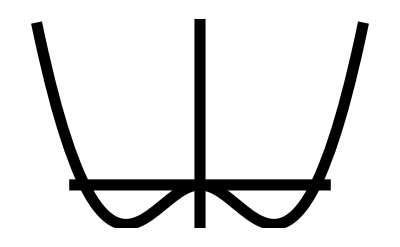

```mathematica
ppv1=Show[Plot[V[q,1/2^(1/2),0.15],{q,-1.5,1.5},PlotStyle->{Black,Thickness[0.02]},Axes->False,Ticks->False,ImagePadding->1],Graphics[{Thickness[0.02],Arrowheads[0.1],Arrow[{{0,-0.6},{0,0.2}}]}],Graphics[{Thickness[0.02],Arrowheads[0.1],Arrow[{{-1.2,-0.5},{1.2,-0.5}}]}]]
```

```mathematica
ppv2=Show[Plot[V[q,1/2^(1/2),-0.15],{q,-1.5,1.5},PlotStyle->{Black,Thickness[0.02]},Axes->False,Ticks->False,ImagePadding->1],Graphics[{Thickness[0.02],Arrowheads[0.1],Arrow[{{0,-0.6},{0,0.2}}]}],Graphics[{Thickness[0.02],Arrowheads[0.1],Arrow[{{-1.2,-0.5},{1.2,-0.5}}]}]]
```

-Graphics-

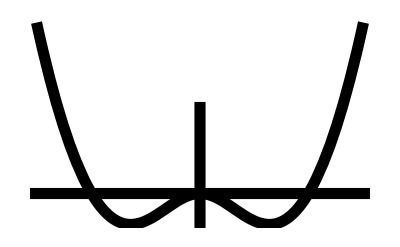

```mathematica
ppv3=Show[Plot[V[q,2/2^(1/2),0.15],{q,-1.6,1.6},PlotStyle->{Black,Thickness[0.02]},Axes->False,ImagePadding->1],Graphics[{Thickness[0.02],Arrowheads[0.1],Arrow[{{0,-0.65},{0,-0.35}}]}],Graphics[{Thickness[0.02],Arrowheads[0.1],Arrow[{{-1.7,-0.5},{1.7,-0.5}}]}]]
```

```mathematica
ppv4=Show[Plot[V[q,2/2^(1/2),-0.15],{q,-1.6,1.6},PlotStyle->{Black,Thickness[0.02]},Axes->False,ImagePadding->1],Graphics[{Thickness[0.02],Arrowheads[0.1],Arrow[{{0,-0.65},{0,-0.35}}]}],Graphics[{Thickness[0.02],Arrowheads[0.1],Arrow[{{-1.7,-0.5},{1.7,-0.5}}]}]]
```

-Graphics-

```mathematica
ppv5=Show[Plot[V[q,1.15,0.15],{q,-1.5,1.5},PlotStyle->{Black,Thickness[0.02]},Axes->False,Ticks->False,ImagePadding->1],Graphics[{Thickness[0.02],Arrowheads[0.1],Arrow[{{0,-0.6},{0,0.2}}]}],Graphics[{Thickness[0.02],Arrowheads[0.1],Arrow[{{-1.2,-0.5},{1.2,-0.5}}]}]]
```

-Graphics-

```mathematica
ppv6=Show[Plot[V[q,1.15,-0.15],{q,-1.5,1.5},PlotStyle->{Black,Thickness[0.02]},Axes->False,Ticks->False,ImagePadding->1],Graphics[{Thickness[0.02],Arrowheads[0.1],Arrow[{{0,-0.6},{0,0.2}}]}],Graphics[{Thickness[0.02],Arrowheads[0.1],Arrow[{{-1.2,-0.5},{1.2,-0.5}}]}]]
```

-Graphics-

```mathematica
L1={{1.0,0},{1.05,0.018},{1.1,0.04},{1.2,0.14},{1.3,0.27},{1.4,0.42},{1.5,0.6},{1.6,0.81},{1.7,1.04},{1.8,1.29},{1.9,1.57},{2.0,1.87},{2.1,2.19},{2.2,2.53},{2.3,2.90},{2.4,3.29},{2.5,3.70}};
L2={{1.0,0},{1.05,-0.018},{1.1,-0.04},{1.2,-0.14},{1.3,-0.27},{1.4,-0.42},{1.5,-0.6},{1.6,-0.81},{1.7,-1.04},{1.8,-1.29},{1.9,-1.57},{2.0,-1.87},{2.1,-2.19},{2.2,-2.53},{2.3,-2.90},{2.4,-3.29},{2.5,-3.7}};
```

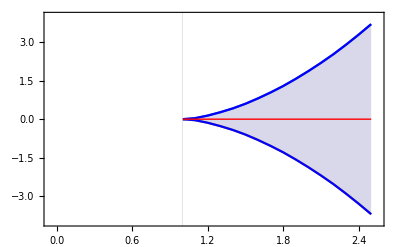

```mathematica
ffondo=Show[ListLinePlot[{L1,L2},Frame->True,PlotRange->{{-0.05,2.55},{-4,4}},GridLines->{{1},{}},GridLinesStyle->{{Black,Dashed,Thick},{}},LabelStyle->{Black,13},Filling->{1->{2}},FillingStyle->{Opacity[0.2],Hue[0.67,0.6,0.6]}],ListPlot[{L1,L2},Joined->True,PlotStyle->Blue],Plot[0,{x,1,2.5},PlotStyle->{Red,Thick}]]
```

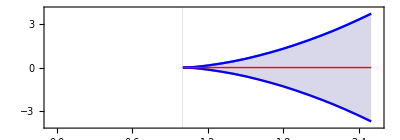
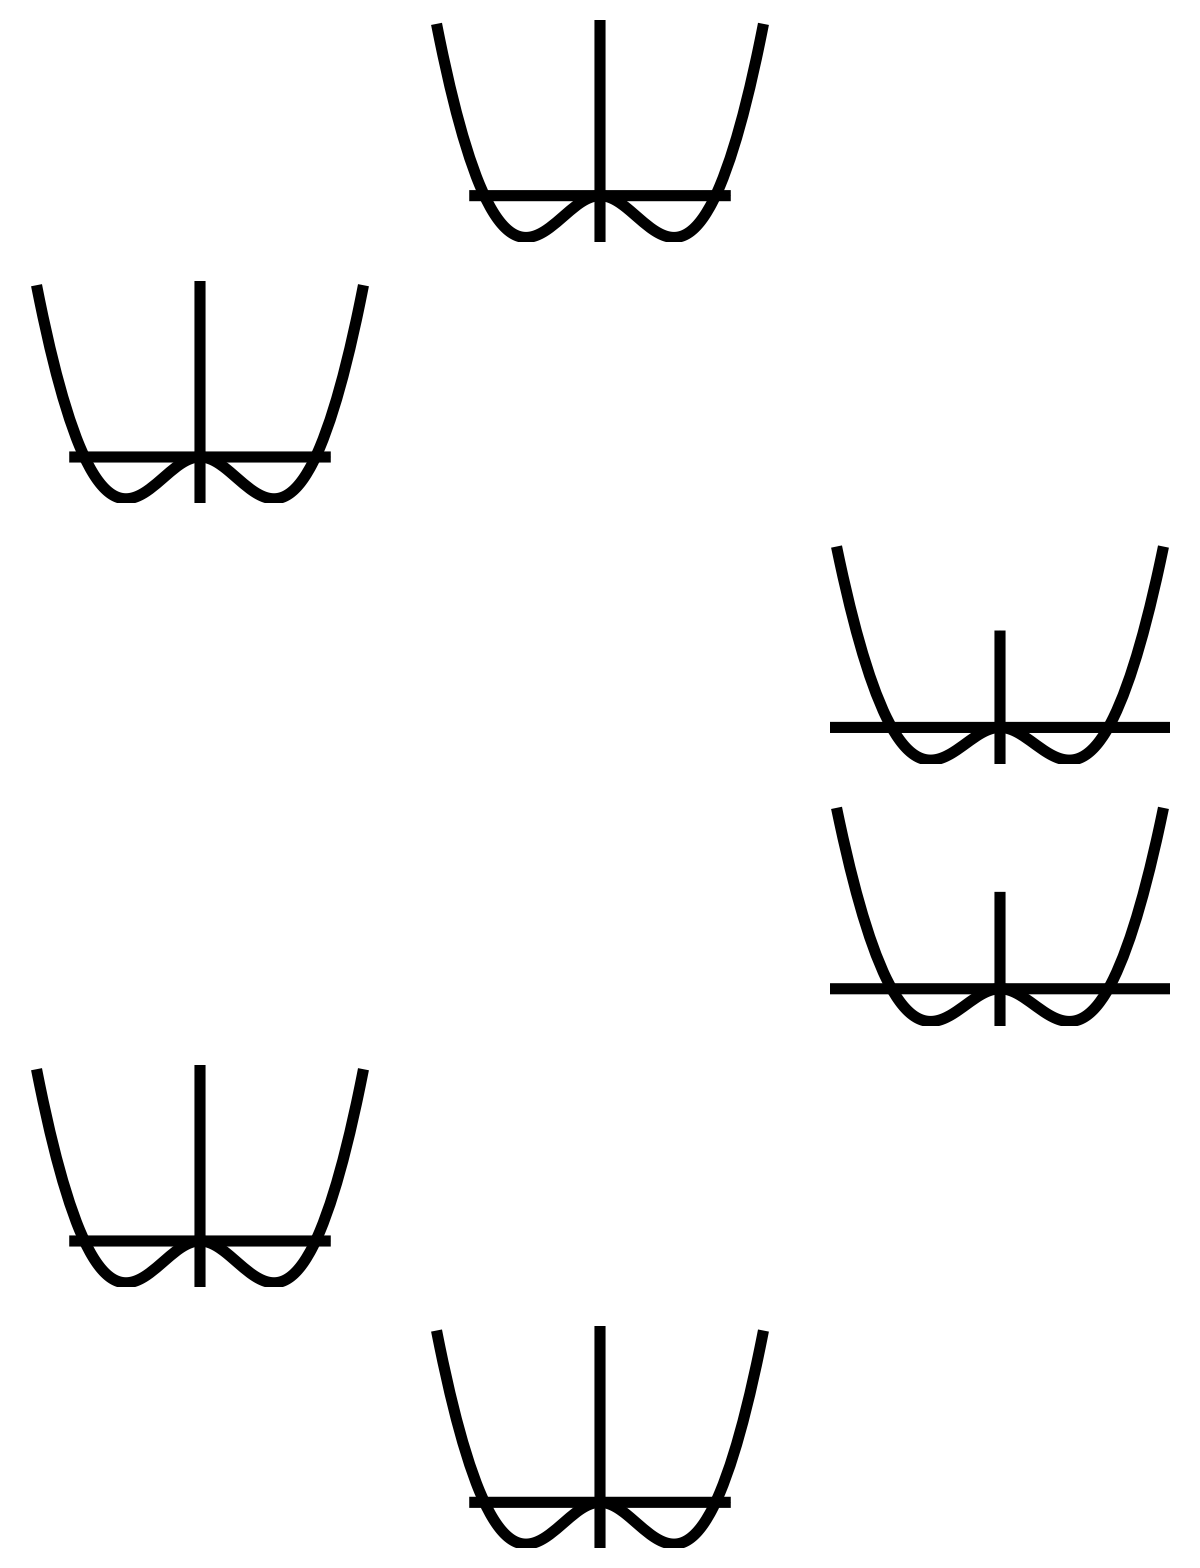

```mathematica
Fases=Show[ffondo,Graphics@Inset[ppv1,{0.25,1.25},{Left,Bottom},Scaled[1/5]],Graphics@Inset[ppv2,{0.25,-2.25},{Left,Bottom},Scaled[1/5]],Graphics@Inset[ppv3,{1.95,0.1},{Left,Bottom},Scaled[1/5]],Graphics@Inset[ppv4,{1.95,-1.9},{Left,Bottom},Scaled[1/5]],Graphics@Inset[ppv5,{1.25,1.75},{Left,Bottom},Scaled[1/5]],Graphics@Inset[ppv6,{1.25,-3},{Left,Bottom},Scaled[1/5]],
AspectRatio->0.35]
```

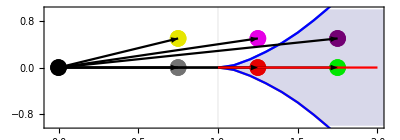

```mathematica
qch=Show[ListLinePlot[{L1,L2},Frame->True,PlotRange->{{-0.05,2},{-1,1}},LabelStyle->{Black,13},Filling->{1->{2}},GridLines->{{1},{}},GridLinesStyle->{{Black,Dashed,Thick},{}},FillingStyle->{Opacity[0.2],Hue[0.67,0.6,0.6]}],ListPlot[{L1,L2},Joined->True,PlotStyle->Blue],ListPlot[{{3/4,0}},PlotStyle->{Darker[Gray,0.1],PointSize[0.03]}],ListPlot[{{5/4,0}},PlotStyle->{Darker[Red,0.1],PointSize[0.03]}],ListPlot[{{7/4,0}},PlotStyle->{Darker[Green,0.1],PointSize[0.03]}],ListPlot[{{3/4,1/2}},PlotStyle->{Darker[Yellow,0.1],PointSize[0.03]}],ListPlot[{{5/4,1/2}},PlotStyle->{Darker[Magenta,0.1],PointSize[0.03]}],ListPlot[{{7/4,1/2}},PlotStyle->{Darker[Purple,0.1],PointSize[0.03]}],ListPlot[{{0,0.0}},PlotStyle->{Black,PointSize[0.03]}],Graphics[{Thickness[0.004],Arrowheads[0.035],Arrow[{{0,0},{3/4,0}}]}],Graphics[{Thickness[0.004],Arrowheads[0.035],Arrow[{{0,0},{5/4,1/2}}]}],
Graphics[{Thickness[0.004],Arrowheads[0.035],Arrow[{{0,0},{3/4,1/2}}]}],Graphics[{Thickness[0.004],Arrowheads[0.035],Arrow[{{0,0},{5/4,0}}]}],Graphics[{Thickness[0.004],Arrowheads[0.035],Arrow[{{0,0},{7/4,0}}]}],Graphics[{Thickness[0.004],Arrowheads[0.035],Arrow[{{0,0},{7/4,1/2}}]}],Plot[0,{x,1,2},PlotStyle->{Red}],AspectRatio->0.35]
```

## Figure 2

```mathematica
(**** AQRM Hamiltonian ***)
g=5/4;
λ=0.0;
HAQRM[q_,p_,t_]=(p^2+q^2)/2-(1/2)*(1+(λ+2^(1/2)*g*q)^2)^(1/2);
```

```mathematica
(*** Classical Phase space contours ***)
pin=0.01;
qin=0.0;
tf=100;
solt=NDSolve[{D[q[t],t]==D[HAQRM[q[t],p[t],t],p[t]],D[p[t],t]==-D[HAQRM[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
tintt=0.01;
qp=Table[{q[t],p[t]}/. solt[[1]]/. t->i,{i,0,tf,tintt}];
```

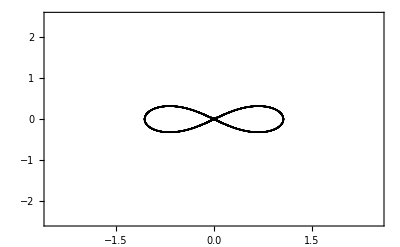

```mathematica
figsep=ListPlot[{qp},PlotStyle->{Black},Axes
->False,Frame->True,PlotRange->{{-2.5,2.5},{-2.5,2.5}},LabelStyle->{16,Black}]
```

```mathematica
(*Importing data from Julia for Wigner function*)
datawigner=Import["../../src/output/wigner_rhot_data.dat"];
datwignorm={};
Do[AppendTo[datwignorm,datawigner[[i]]];
If[datwignorm[[i,3]]<0,datwignorm[[i,3]]=2*datwignorm[[i,3]]],{i,1,Length[datawigner]}]
```

```mathematica
(*Color for the Wigner function*)
FCo[t_]=Piecewise[{{ RGBColor[1,(2t)^3,(2t)^3],0<=t<=1/2},{ RGBColor[(1-2(t-1/2)),(1-2(t-1/2)),1],1/2<t<=1}}];
```

```mathematica
fac=0.5/0.35;
wigner2=Show[ListDensityPlot[datwignorm,PlotRange->{{-2.5,2.5},{-2.5,2.5},All},Frame->True,LabelStyle->{Black,22},ColorFunction->(FCo[1-fac*(#+0.35)]&),ColorFunctionScaling->False(*,PlotLegends->Automatic*)],figsep]
```

-Graphics-

## Figure 3

```mathematica
θmax=12;
r=10;
data=Import["../../src/output/Loschmidt_amplitud.dat"];
datneg=Import["../../src/output/negativities_quench.dat"];
datneg1b=Table[{datneg[[i,1]],datneg[[i,2]]},{i,1,Length[datneg]}];
datneg2b=Table[{datneg[[i,1]],datneg[[i,3]]},{i,1,Length[datneg]}];
datfis=Import["../../src/output/qfi_quench.dat"];
datfisher=Table[{datfis[[i,1]],datfis[[i,4]]},{i,1,Length[datfis]}];
datcrosst=Import["../../src/output/zeros_cutwigner.dat"];
datscrossb=Table[{datcrosst[[i,1]],datcrosst[[i,θmax]]},{i,1,Length[datcrosst]}];
datac=Import["../../src/output/Loschmidt_amplitud_ct.dat"];
ampcomp=Table[data[[i,2]]+I*data[[i,3]],{i,1,Length[data]}];
dataRate=Table[{data[[i,1]],-Log[Abs[ampcomp[[i]]]^2]/r},{i,1,Length[data]}];
ampcomp=Table[datac[[i,3]]+I*datac[[i,4]],{i,1,Length[datac]}];
datact=Table[{datac[[i,1]],datac[[i,2]],Log[Abs[ampcomp[[i]]]^2]},{i,1,Length[datac]}];
```

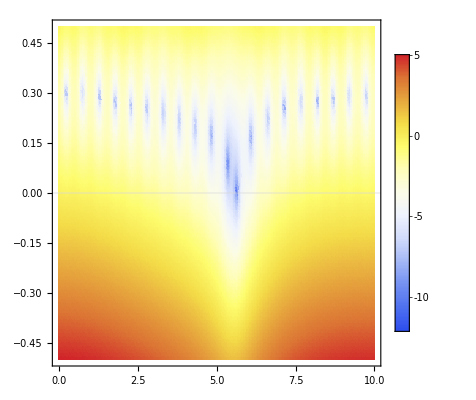

```mathematica
(*First column*)
ListDensityPlot[datact,GridLines->{{},{0}},LabelStyle->{22,Black},GridLinesStyle->{{Dashed,Black,Thick},{Thick,Black,Dashed}},PlotRange->{{0,10},{-0.5,0.5},{-30,20}},PlotLegends->Automatic,ColorFunction->"TemperatureMap",LabelStyle->"Subtitle"]
```

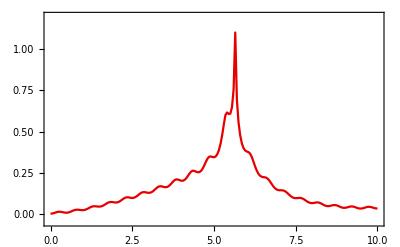

```mathematica
(*Second column*)
ListPlot[{dataRate},PlotRange->{{0,10},{-0.05,1.2}},Joined->True,PlotStyle->{Darker[Red,0.1]},Frame->True,LabelStyle->{18,Black},GridLines->{{},{}},PlotLegends->{},GridLinesStyle->{{Dashed,Black,Thickness[0.007]},{Thick,Red,Dashed}}]
```

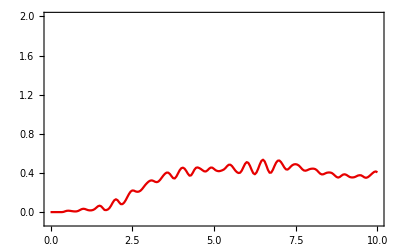

```mathematica
(*Third column*)
ListPlot[{datneg1b},PlotRange->{{0,10},{-0.1,2}},GridLines->{{},{}},GridLinesStyle->{{Dashed,Black,Thickness[0.007]},{}},Frame->True,Joined->True,PlotStyle->{Darker[Red,0.1]},LabelStyle->{Black,18}]
```

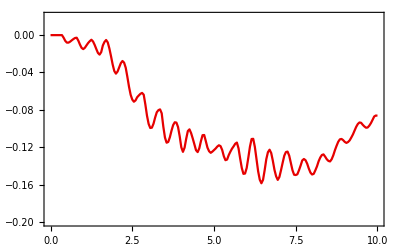

```mathematica
(*Fourth column*)
ListPlot[{datneg2b},PlotRange->{{0,10},{-0.2,0.02}},GridLines->{{},{}},GridLinesStyle->{{Dashed,Black,Thickness[0.007]},{}},Frame->True,Joined->True,PlotStyle->{Darker[Red,0.1]},LabelStyle->{Black,18}]
```

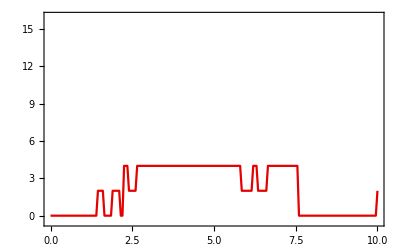

```mathematica
(*Fifth column*)
ListPlot[{datscrossb},PlotRange->{{0,10},{-0.5,16}},GridLines->{{},{}},GridLinesStyle->{{Dashed,Black,Thickness[0.007]},{}},Frame->True,Joined->True,PlotStyle->{Darker[Red,0.1]},LabelStyle->{Black,18}]
```

## Figure 4

### TWA

```mathematica
(*Initial Wigner function for TWA*)
q0=0.0;p0=0.0;
(*semiclassical parameter*)
r=10;
d[q_,p_]=Sqrt[(q-q0)^2+(p-p0)^2];
Wqp[q_,p_]= r/π Exp[-r*d[q,p]^2];
W[q_,p_]= Wqp[q,p];
```

```mathematica
(*Replicating initial state in the classical phase space*)
Δx=0.05;Δy=0.05; 
LX=15;LY=15; 
Qo=0;Po=0;
hps=Flatten[Table[{x,y},{x,Qo-LX,Qo+LX,Δx},{y,Po-LY,Po+LY,Δy}],1];
wliqp=Table[Wqp[hps[[k,1]],hps[[k,2]]],{k,1,Length[hps]}];
NR=10000; (*Number of points for TWA *)
ralqp=RandomChoice[wliqp->hps,NR];
```

General::munfl: Exp[-4500.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4485.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4470.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

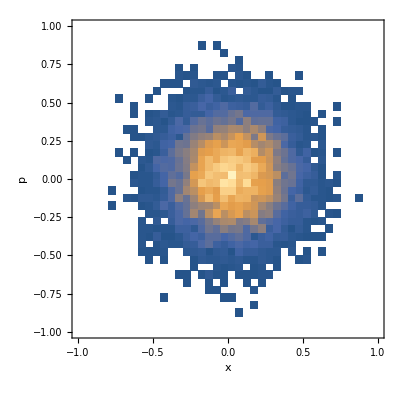

```mathematica
Show[DensityHistogram[ralqp,30,PlotRange->{{-1,1},{-1,1}},AxesLabel->{"x","p"}]]
```

```mathematica
(*** Solving classical equations for motion for the TWA**)
ti=0;
tf=10.0;
tint=0.05;
g=5/4;(*coupling*)
λ=0.0;(*asymmetry bias*)
HAQRM[q_,p_,t_]=(p^2+q^2)/2-(1/2)*(1+(λ+2^(1/2)*g*q)^2)^(1/2);
eqsmov={};
eps=0.01;
Monitor[Do[
eqsmovinst={};
qin=ralqp[[k,1]];
pin=ralqp[[k,2]];
sol=NDSolve[{D[q[t],t]==D[HAQRM[q[t],p[t],t],p[t]],D[p[t],t]==-D[HAQRM[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
Do[QPinst={q[i],p[i]}/.sol;
qinst=QPinst[[1,1]];
pinst=QPinst[[1,2]];
AppendTo[eqsmovinst,{qinst,pinst}],{i,ti,tf,tint}];
AppendTo[eqsmov,eqsmovinst],{k,1,Length[ralqp]}],N[k/Length[ralqp]]]
```

```mathematica
(*Importing exact survial amplitude from Julia*)
data=Import["../../src/output/Loschmidt_amplitud.dat"];
```

```mathematica
SPb=Table[{(t-1)*tint,(2π )^1* Sum[Wqp[eqsmov[[k,t,1]],eqsmov[[k,t,2]]],{k,t,NR}]/(NR*r)},{t,1,200}];
ampcomp=Table[data[[i,2]]+I*data[[i,3]],{i,1,Length[data]}];
dataRate=Table[{data[[i,1]],-Log[Abs[ampcomp[[i]]]^2]/r},{i,1,Length[data]}];
dataRateTWA=Table[{SPb[[i,1]],-Log[Abs[SPb[[i,2]]]]/r},{i,1,Length[SPb]}];
```

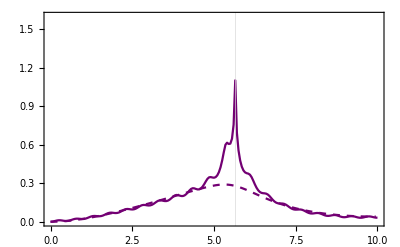

```mathematica
figLE=ListPlot[{dataRate,dataRateTWA},PlotRange->{{0,10},{-0.001,1.6}},PlotLegends->{},Axes->False,PlotStyle->{Darker[Purple,0.1],{Darker[Purple,0.1],Dashed}},Frame->True,Joined->{True,True},LabelStyle->{16,Black},FrameLabel->{},GridLines->{{5.66},{}},GridLinesStyle->{{Black,Dashed,Thickness[0.007]},{Thick,Red,Dashed}}]
```

### Histogram of Points for TWA

```mathematica
shot=94;
Listaqpt=Table[{eqsmov[[k,shot,1]],eqsmov[[k,shot,2]]},{k,1,Length[ralqp]}];
```

```mathematica
(*Shot inicial para referencia*)
shotInicial=1;
(*Lista de puntos iniciales*)
listaQPini=Table[{eqsmov[[k,shotInicial,1]],eqsmov[[k,shotInicial,2]]},{k,Length[ralqp]}];
(*Crear distribución de kernel*)
distIni=SmoothKernelDistribution[listaQPini];
(*Evaluar densidad máxima para normalizar*)
ρmax=Max[PDF[distIni,#]&/@listaQPini];
```

```mathematica
(*** Classical Phase space contours ***)
pin=0.01;
qin=0.0;
tf=100;
solt=NDSolve[{D[q[t],t]==D[HAQRM[q[t],p[t],t],p[t]],D[p[t],t]==-D[HAQRM[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
tintt=0.01;
qp=Table[{q[t],p[t]}/. solt[[1]]/. t->i,{i,0,tf,tintt}];
```

```mathematica
figsep=ListPlot[{qp},PlotStyle->{Black},Axes
->False,Frame->True,PlotRange->{{-2.5,2.5},{-2.5,2.5}},LabelStyle->{16,Black}]
```

-Graphics-

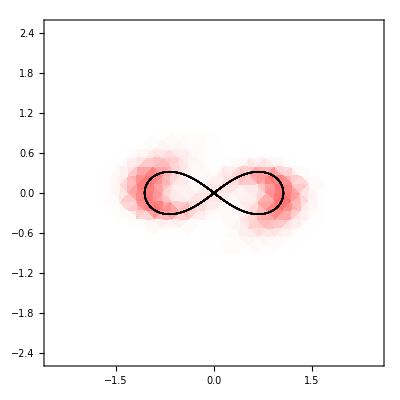

```mathematica
fac=0.5;
tshot=Show[SmoothDensityHistogram[Listaqpt,PlotRange->{{-2.5,2.5},{-2.5,2.5}},LabelStyle->{Black,22},ColorFunction->(Blend[{White,Red},#/(fac*ρmax)]&),(*PlotLegends->Placed[BarLegend[{Blend[{White,Red},#/(0.25*ρmax)]&,{0,fac*ρmax}}],Right],*)PerformanceGoal->"Quality",PlotPoints->20,MaxRecursion->1],figsep]
```

### Exact Wigner function

```mathematica
(*Importing data from Julia for Wigner function*)
datawigner=Import["../../src/output/wigner_rhot_data.dat"];
datwignorm={};
Do[AppendTo[datwignorm,datawigner[[i]]];
If[datwignorm[[i,3]]<0,datwignorm[[i,3]]=2*datwignorm[[i,3]]],{i,1,Length[datawigner]}]
```

```mathematica
(*Color for the Wigner function*)
FCo[t_]=Piecewise[{{ RGBColor[1,(2t)^3,(2t)^3],0<=t<=1/2},{ RGBColor[(1-2(t-1/2)),(1-2(t-1/2)),1],1/2<t<=1}}];
```

```mathematica
fac=0.5/0.35;
wigner2=Show[ListDensityPlot[datwignorm,PlotRange->{{-2.5,2.5},{-2.5,2.5},All},Frame->True,LabelStyle->{Black,22},ColorFunction->(FCo[1-fac*(#+0.35)]&),ColorFunctionScaling->False(*,PlotLegends->Automatic*)],figsep]
```

-Graphics-